Two Photon and Nonlinear refraction Dispersion AlxGa1-xAs
Prof. Charlie Ironside
Department of Physics and Astronomy
Curtin University 
Bentley Campus,
Western Australia 6102
email: Charlie.Ironside@curtin.edu.au
web page address:http://oasisapps.curtin.edu.au/staff/profile/view/Charlie.Ironside
 
 Included in the book : “Semiconductor Integrated Optics for Switching Light” by Charlie Ironside 
 see :-
  M. J. LaGasse et al “Femtosecond measurements of the nonresonant nonlinear index in AlGAAs”, Apple Phys. Lett., 56 417-419-1990
 Sheik Bahae et al “Dispersion of bound electronic nonlinear refraction in solids “, IEEE Journal of Quantum Electronics 1991 27 1296-1309.
 E. W. Vanstryland, H. Vanherzeele, M. A. Woodall, M. J. Soileau, A. L. Smirl, S. Guha, et al., “2 Photon-Absorption, Nonlinear Refraction, and Optical Limiting in Semiconductors,” Optical Engineering, vol. 24, pp. 613-623, 1985  http://dx.doi.org/10.1117/12.7973538
 The conversion of units from ESU to SI for n2 can be found at:-
 https://www.rp-photonics.com/nonlinear_index.html
 The dependence of the Al_x Ga_(1-x)As alloy band-gap on x can be found at:-
http://www.semiconductors.co.uk/eg(algaas).htm

```mathematica
TwoAxisPlot[{f_,g_},{x_,x1_,x2_}]:=Module[{fgraph,ggraph,frange,grange,fticks,gticks},{fgraph,ggraph}=MapIndexed[Plot[#,{x,x1,x2},Axes->True,PlotStyle->ColorData[1][#2[[1]]]]&,{f,g}];{frange,grange}=(PlotRange/.AbsoluteOptions[#,PlotRange])[[2]]&/@{fgraph,ggraph};fticks=N@FindDivisions[frange,5];
gticks=Quiet@Transpose@{fticks,ToString[NumberForm[#,2],StandardForm]&/@Rescale[fticks,frange,grange]};
Show[fgraph,ggraph/.Graphics[graph_,s___]:>Graphics[GeometricTransformation[graph,RescalingTransform[{{0,1},grange},{{0,1},frange}]],s],Axes->False,Frame->True,FrameStyle->{ColorData[1]/@{1,2},{Automatic,Automatic}},FrameTicks->{{fticks,gticks},{Automatic,Automatic}}]]
```

1347.03/λ

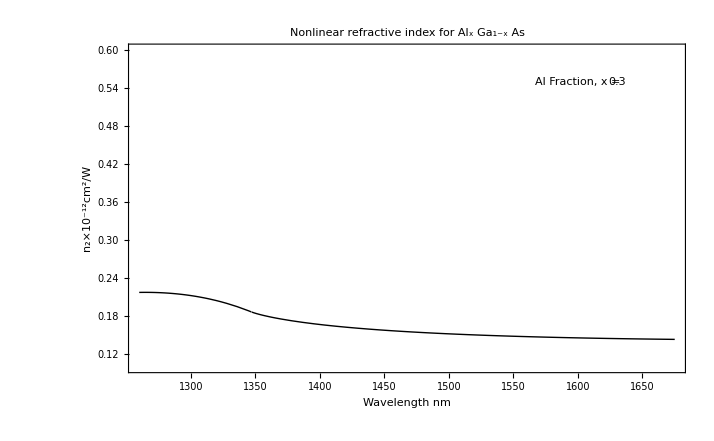

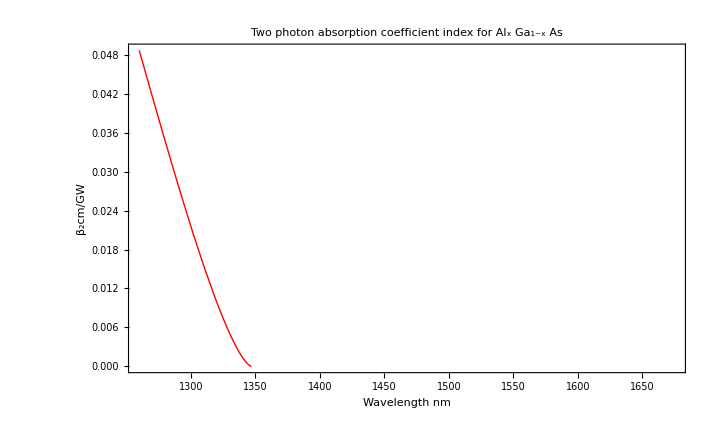

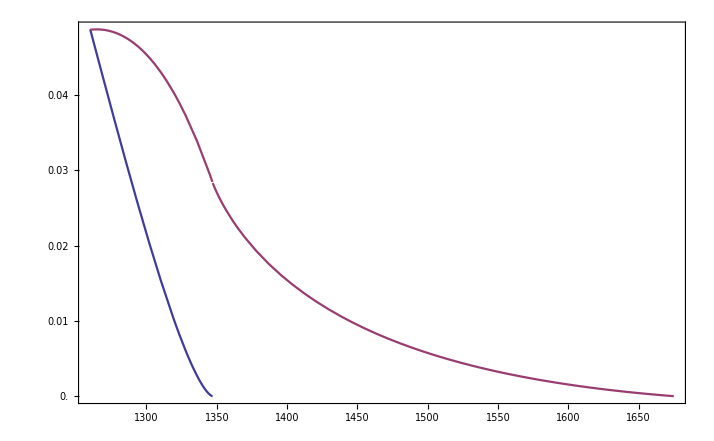

```mathematica
ClearAll[x,CLight,Echarge,PlanckCon,G2,n2,β2,Ep]
x=0.30 ;(*input Subscript[Al, x] Subscript[Ga, 1-x] As alloy Al fraction - don't go above x=0.44 or it goes indirect and all bets are off*) 
n:=3.43 ;(* refractive index just assumed as constant*)
CLight:=299792458 (*speed of light m/s*)
PlanckCon:=6.6×10^-34(*Planck's constant SI units*)
Echarge:=1.6×10^-19(*Charge on the electron, C*)
EG=1.42 +1.429 x-0.14 x^2 ; (*band gap in eV*)
eV:=(PlanckCon*CLight)/(Echarge(λ×10^-9));(* wavelength, λ, in nm*)
Ep=25.7 ;(* eV, see Van Stryland paper for GaAs *)
y=eV/EG; (*required for n2 nonlinear refractive index*)
y2=(2 eV)/EG(*required for β2 two photon absorption coefficient*)
G2=(-2+6y-3 y^2-y^3-3/4 y^4+2(1-2 y)^(3/2)UnitStep[1-2y])/(64 y^6);(*Dispersion of n2 nonlinear refractive index*)
n2=62.8 (Ep^(1/2)G2)/(n^2 EG^4);(*n2×10^-12 in cm^2/W*)
β2:=53.8 Ep^(1/2)/(n^2 EG^3)(y2-1)^(3/2)/y2^5(*dispersion β2 in cm/GW two photon absorption coefficient*)
Plot [n2,{λ,1260, 1675},PlotRange->{0.1,0.6}, PlotLabel->HoldForm[Nonlinear refractive index for Subscript[Al, x] Subscript[Ga, 1-x] As],LabelStyle->{FontFamily->"Times New Roman",14,GrayLevel[0]},GridLines->Full,GridLinesStyle->Directive[Black,Opacity[0.1]],PlotStyle->{Directive[Thick,Black]},Frame->True,FrameLabel->{"Wavelength nm","n_2×10^-12cm^2/W"},FrameStyle->Thick,GridLines->Full,Epilog->{Text["Al Fraction, x =",{1600,0.550}],Text[x,{1630,0.550}]}](* the optical communications channels are effectively 1260-1675nm the c-band is 1530-1565nm*)
Plot [β2,{λ,1260, 1675},PlotLabel->HoldForm[Two photon absorption coefficient index for Subscript[Al, x] Subscript[Ga, 1-x] As],LabelStyle->{FontFamily->"Times New Roman",14,GrayLevel[0]},GridLines->Full,GridLinesStyle->Directive[Black,Opacity[0.1]],PlotStyle->{Directive[Thick,Red]},Frame->True,FrameLabel->{"Wavelength nm","β_2cm/GW"},FrameStyle->Thick,GridLines->Full] (* the optical communications channels are effectively 1260-1675nm the c-band is 1530-1565nm*)
TwoAxisPlot[{β2,n2},{λ,1260, 1675}](*comapre the nonlinear reafrctive index and the two photon absorption coefficient in the same plot*)
```